Импортируем данные:

```mathematica
data={{1,2,11},{1,5,12},{1,6,5},{1,8,4},{1,9,7},{1,10,8},{1,11,8},{1,12,11},{1,13,10},{1,16,4},{2,8,5},{2,25,5},{5,19,8},{5,21,6},{6,8,10},{6,11,6},{8,12,7},{8,19,6},{8,23,7},{9,19,5},{9,37,4},{10,24,9},{10,38,4},{11,12,12},{11,22,9},{11,35,5},{12,24,6},{12,25,5},{12,26,12},{13,24,4},{13,31,4},{16,19,10},{16,26,6},{19,21,12},{19,22,12},{19,33,7},{19,34,6},{21,22,11},{22,29,5},{22,30,4},{22,37,6},{23,24,5},{24,26,10},{24,31,4},{24,33,5},{25,26,8},{26,29,7},{26,30,8},{26,34,12},{26,38,7},{29,40,11},{29,42,6},{30,36,5},{30,40,7},{31,34,8},{33,40,11},{33,45,8},{34,38,10},{34,40,9},{34,42,5},{35,36,4},{35,45,12},{36,45,4},{37,45,8},{38,40,7},{38,44,5},{38,45,7},{40,44,9},{40,45,9},{42,45,9},{44,45,10}};
```

```mathematica
vertices = Union[Flatten[data[[All,{1,2}]]]];
```

```mathematica
edges =DirectedEdge@@@data[[All, {1,2}]];
```

```mathematica
weights = data[[All,3]];
```

Строим граф:

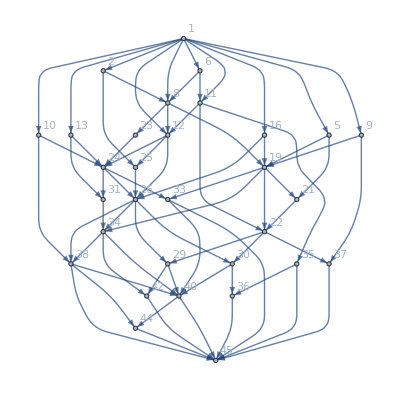

```mathematica
g = Graph[vertices,edges,VertexLabels->Automatic,EdgeCapacity->weights]
```

Найдем максимальный поток в сети:

```mathematica
flow= FindMaximumFlow[g, 1, 45, "OptimumFlowData"]
```

OptimumFlowData[…]

```mathematica
maxflow = flow["FlowValue"]
```

60

Таким образом максимальный поток - 60. Построим минимальный разрез в сети.

```mathematica
mincut = FindMinimumCut[g]
```

{0,{{35,36,37,42,45},{1,2,5,6,8,9,10,11,12,13,16,19,21,22,23,24,25,26,29,30,31,33,34,38,40,44}}}

Две несвязные части графа выделены желтым и красным цветами соответственно.

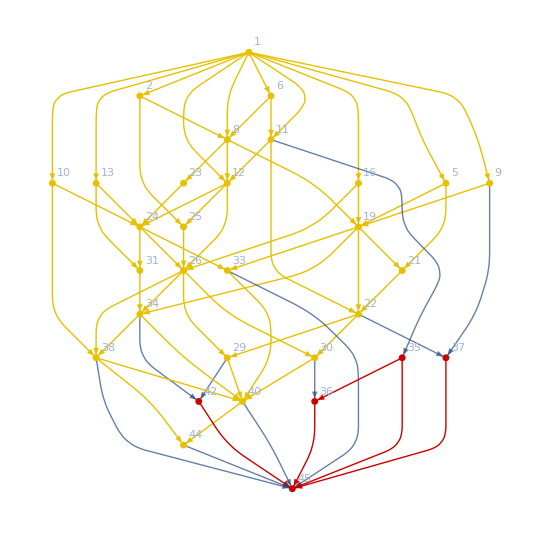

```mathematica
HighlightGraph[g,Map[Subgraph[g,#]&,Last[%]]]
```

```mathematica
mincut[[2,2]]
```

{1,2,5,6,8,9,10,11,12,13,16,19,21,22,23,24,25,26,29,30,31,33,34,38,40,44}

```mathematica
flow["FlowGraph"]
```

Отобразим распределение потока по ребрам графа.